Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/pltcm_manipulated_84882.csv"];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/9,1];
{a,b,c,d,e,f,g,h,i}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/19,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t},2,1]}],1]];
win2=Length@data2;
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,11,win1];]
```

{20.4316,Null}

```mathematica
graphsandnodenumbers1=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers1[[i]][[1]],FindGraphCommunities[graphsandnodenumbers1[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers1}];
singlerandomgraphscomm1=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers1[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm1[[i]],FindGraphCommunities[singlerandomgraphscomm1[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm1}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers1[[All,1]]}];]
```

{310.91,Null}

```mathematica
bucketnode11=Round@N@Mean@graphsandnodenumbers1[[All,2]]
```

82

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,9,11,win2];]
```

{20.8213,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
singlerandomgraphscomm12=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
AbsoluteTiming[Zscoresmodularity12=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{692.787,Null}

```mathematica
bucketnode12=Round@N@Mean@graphsandnodenumbers12[[All,2]]
```

76

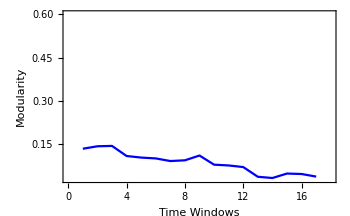
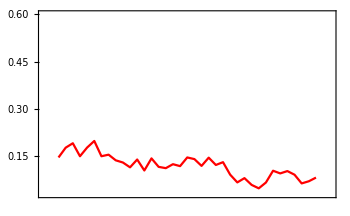
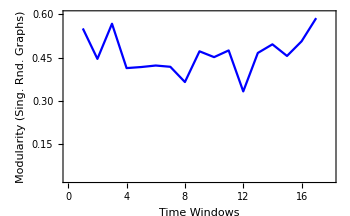
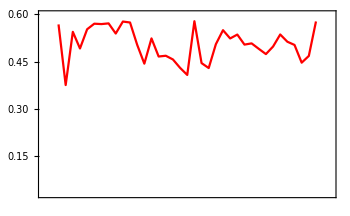
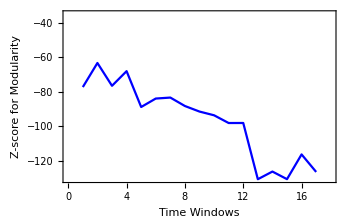
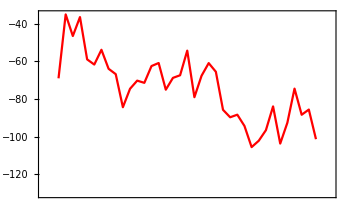

```mathematica
modularityplotrange={0.03,0.6};(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues12,singlerandomcommmodularityvalues12}]*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues12}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues12}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1,Zscoresmodularity12}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity12}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1,Zscoresmodularity12}]}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,0.05,win1];]
```

{9.29178,Null}

```mathematica
graphsandnodenumbers2=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers2[[i]][[1]],FindGraphCommunities[graphsandnodenumbers2[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers2}];
singlerandomgraphscomm2=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers2[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm2[[i]],FindGraphCommunities[singlerandomgraphscomm2[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm2}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers2[[All,1]]}];]
```

{166.087,Null}

```mathematica
bucketnode21=Round@N@Mean@graphsandnodenumbers2[[All,2]]
```

49

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,10,0.05,win2];]
```

{9.0299,Null}

```mathematica
graphsandnodenumbers22=Table[snetworkgraph[thicknessdataintimewindowsFixedstep2[[1]][[i]],thicknessdataintimewindowsFixedstep2[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues22=Table[N@GraphAssortativity[graphsandnodenumbers22[[i]][[1]],FindGraphCommunities[graphsandnodenumbers22[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers22}];
singlerandomgraphscomm22=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers22[[All,1]]}];
singlerandomcommmodularityvalues22=Table[N@GraphAssortativity[singlerandomgraphscomm22[[i]],FindGraphCommunities[singlerandomgraphscomm22[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm22}];
AbsoluteTiming[Zscoresmodularity22=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers22[[All,1]]}];]
```

{303.611,Null}

```mathematica
bucketnode22=Round@N@Mean@graphsandnodenumbers22[[All,2]]
```

44

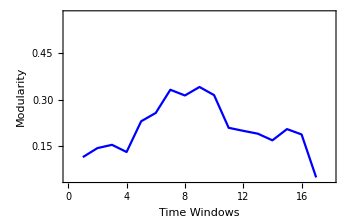
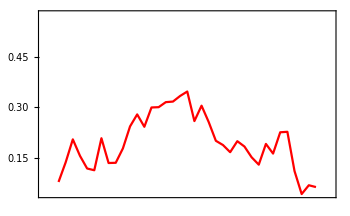
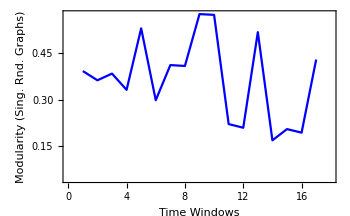
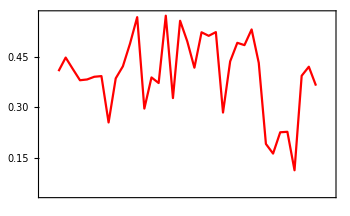
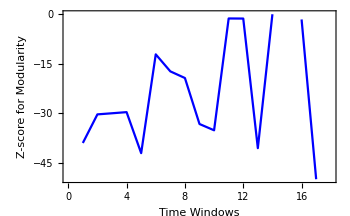
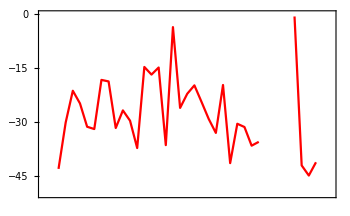

```mathematica
modularityplotrange=MinMax[{modularityvalues2,singlerandomcommmodularityvalues2,modularityvalues22,singlerandomcommmodularityvalues22}];
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues22}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues22}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity2/.Indeterminate->0,Zscoresmodularity22/.Indeterminate->0}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity22}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity2/.Indeterminate->0,Zscoresmodularity22/.Indeterminate->0}]}]}]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,9,bucketnode11,win1];]
```

{3.68992,Null}

```mathematica
graphsandnodenumbers3=Table[snetworkgraph[widthdataintimewindowsFixedbucket1[[1]][[i]],widthdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,Green],{i,Range@win1}];
modularityvalues3=Table[N@GraphAssortativity[graphsandnodenumbers3[[i]][[1]],FindGraphCommunities[graphsandnodenumbers3[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers3}];
singlerandomgraphscomm3=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers3[[All,1]]}];
singlerandomcommmodularityvalues3=Table[N@GraphAssortativity[singlerandomgraphscomm3[[i]],FindGraphCommunities[singlerandomgraphscomm3[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm3}];
AbsoluteTiming[Zscoresmodularity3=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers3[[All,1]]}];]
```

{515.438,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,9,bucketnode12,win2];]
```

{4.79545,Null}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
singlerandomgraphscomm32=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
AbsoluteTiming[Zscoresmodularity32=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{744.409,Null}

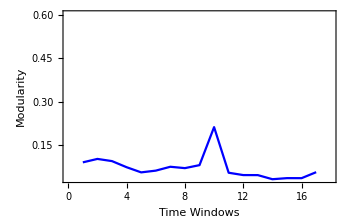
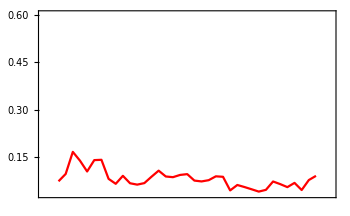
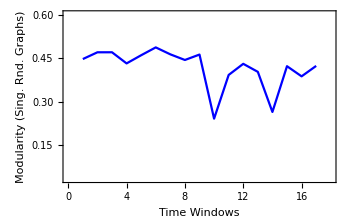
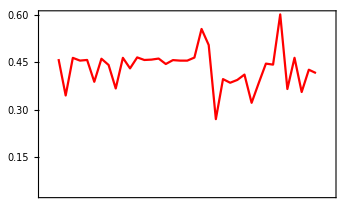
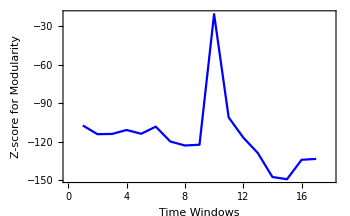
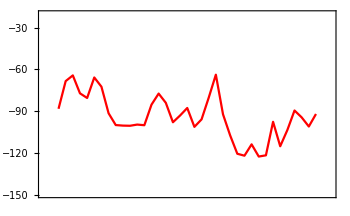

```mathematica
modularityplotrange=MinMax[{modularityvalues3,singlerandomcommmodularityvalues3,modularityvalues32,singlerandomcommmodularityvalues32}];
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues3}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues32}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues3}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues32}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity3}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity3,Zscoresmodularity32}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity32}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity3,Zscoresmodularity32}]}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,10,bucketnode21,win1];]
```

{3.20013,Null}

```mathematica
graphsandnodenumbers4=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket1[[1]][[i]],thicknessdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues4=Table[N@GraphAssortativity[graphsandnodenumbers4[[i]][[1]],FindGraphCommunities[graphsandnodenumbers4[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers4}];
singlerandomgraphscomm4=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers4[[All,1]]}];
singlerandomcommmodularityvalues4=Table[N@GraphAssortativity[singlerandomgraphscomm4[[i]],FindGraphCommunities[singlerandomgraphscomm4[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm4}];
AbsoluteTiming[Zscoresmodularity4=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers4[[All,1]]}];]
```

{184.279,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,10,bucketnode22,win2];]
```

{3.26835,Null}

```mathematica
graphsandnodenumbers42=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket2[[1]][[i]],thicknessdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues42=Table[N@GraphAssortativity[graphsandnodenumbers42[[i]][[1]],FindGraphCommunities[graphsandnodenumbers42[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers42}];
singlerandomgraphscomm42=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers42[[All,1]]}];
singlerandomcommmodularityvalues42=Table[N@GraphAssortativity[singlerandomgraphscomm42[[i]],FindGraphCommunities[singlerandomgraphscomm42[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm42}];
AbsoluteTiming[Zscoresmodularity42=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers42[[All,1]]}];]
```

{423.502,Null}

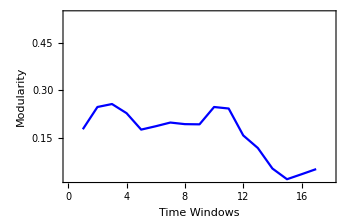
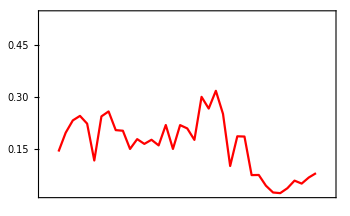
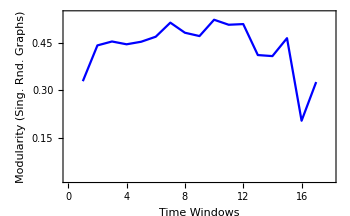
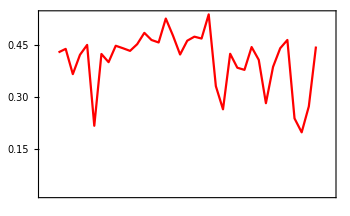
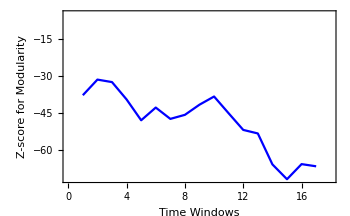
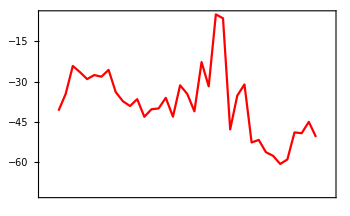

```mathematica
modularityplotrange=MinMax[{modularityvalues4,singlerandomcommmodularityvalues4,modularityvalues42,singlerandomcommmodularityvalues42}];
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues4}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues42}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues4}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues42}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity4}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity4,Zscoresmodularity42}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity42}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity4,Zscoresmodularity42}]}]}]}
```